```mathematica
f[αa_,P_]= P Sin[αa]/αa+Cos[αa]
```

Cos[αa]+(P Sin[αa])/αa

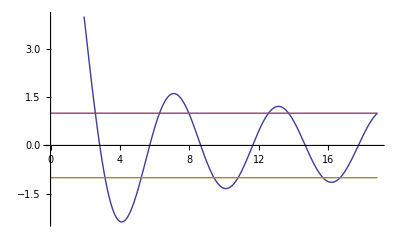

```mathematica
Plot[{f[αa,9],y=1,y=-1},{αa,0,6π}]
```

```mathematica
FindRoot[f[αa,9]==1,{αa,2,3}]
```

{αa→2.58268}

```mathematica
EofJ[αa_,a_]=αa^2/a^2 ((1.054*10^-34)^2)/(2(9.11*10^-31))
```

(6.09723×10^-39 αa^2)/a^2

```mathematica
EofeV[αa_,a_]=αa^2/a^2 ((1.054*10^-34)^2)/(2(9.11*10^-31)) 1/(1.60217646*10^-19)
```

(3.80559×10^-20 αa^2)/a^2

```mathematica
EofeV[2.58268,5*10^-10]
```

1.01537

```mathematica
FindRoot[f[αa,9]==-1,{αa,3,3.5}]
```

{αa→3.14159}

```mathematica
EofeV[3.14159,5*10^-10]
```

1.50239

```mathematica
FindRoot[f[αa,9]==-1,{αa,5,5.5}]
```

{αa→5.23031}

```mathematica
EofeV[5.23031,5*10^-10]
```

4.16426

```mathematica
FindRoot[f[αa,9]==1,{αa,6,6.5}]
```

{αa→6.28319}

```mathematica
EofeV[6.28319,5*10^-10]
```

6.00956

```mathematica
FindRoot[f[αa,9]==1,{αa,7.8,8.5}]
```

{αa→7.97465}

```mathematica
EofeV[7.97465,5*10^-10]
```

9.68068

```mathematica
FindRoot[f[αa,9]==-1,{αa,9,10}]
```

{αa→9.42478}

```mathematica
EofeV[9.42478,5*10^-10]
```

13.5215

```mathematica
FindRoot[f[αa,9]==-1,{αa,10.5,11}]
```

{αa→10.8131}

```mathematica
EofeV[10.8131,5*10^-10]
```

17.7985

```mathematica
FindRoot[f[αa,9]==1,{αa,12,13}]
```

{αa→12.5664}

```mathematica
EofeV[12.5664,5*10^-10]
```

24.0383